# Rolling ball dynamics

```mathematica
Quit[];
```

{9.81 m Sin[θ[t]]-1. m x[t] θ'[t]^2+1. m x''[t],9.81 m Sin[ϕ[t]]-1. m y[t] ϕ'[t]^2+1. m y''[t],9.81 m Cos[θ[t]] x[t]+2. m x[t] x'[t] θ'[t]+1. m x[t]^2 θ''[t],9.81 m Cos[ϕ[t]] y[t]+2. m y[t] y'[t] ϕ'[t]+1. m y[t]^2 ϕ''[t]}

{{x''[t]→-9.81 Sin[θ[t]]+1. x[t] θ'[t]^2,y''[t]→-9.81 Sin[ϕ[t]]+1. y[t] ϕ'[t]^2,θ''[t]→(9.81-9.81 Cos[θ[t]]-2. x'[t] θ'[t])/x[t],ϕ''[t]→(9.81-9.81 Cos[ϕ[t]]-2. y'[t] ϕ'[t])/y[t]}}

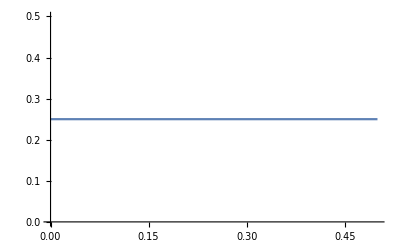

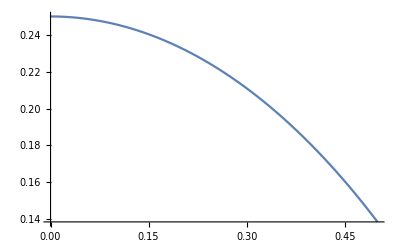

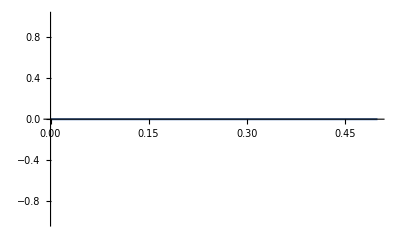

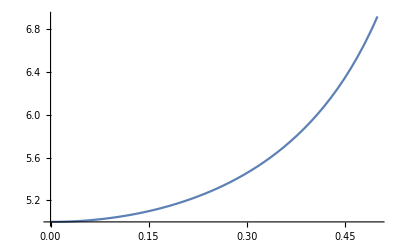

```mathematica
(* Dimensions and Parameters *)
g=9.81;

(* States *)
q={{x[t]},{y[t]},{θ[t]},{ϕ[t]}};
dq=D[q,t];
ddq=D[dq,t];

(* Lagrangian *)
T=0.5*m*(x'[t]^2+y'[t]^2+(x[t]*θ'[t])^2+(y[t]*ϕ'[t])^2);
V=m*g*(x[t]*Sin[θ[t]]+y[t]*Sin[ϕ[t]]);
L=T-V;

(* Euler Lagrange *)
τ1=m*g*x[t];
τ2=m*g*y[t];
EL=(D[D[L,dqᵀ],t]-D[L,qᵀ])
temp=Solve[EL[[1]]==0&&EL[[2]]==0&&EL[[3]]==τ1&&EL[[4]]==τ2,ddqᵀ[[1]]]//Simplify
eq1=ddq[[1,1]]==temp[[1,1,2]];
eq2=ddq[[2,1]]==temp[[1,2,2]];
eq3=ddq[[3,1]]==temp[[1,3,2]];
eq4=ddq[[4,1]]==temp[[1,4,2]];

(* Conditions *)
initCond={x[0]==.25,y[0]==.25,θ[0]==0 Degree,ϕ[0]==5 Degree,x'[0]==0,y'[0]==0,θ'[0]==0,ϕ'[0]==0};

(* NDSolve *)
tf=.5;
sol=NDSolve[Join[{eq1,eq2,eq3,eq4},initCond],{x,y,θ,ϕ},{t,0,tf}];

(* Plotting *)
xsol=x[t]/.sol[[1]];
ysol=y[t]/.sol[[1]];
Plot[x[t]/.sol[[1]],{t,0,tf}]
Plot[y[t]/.sol[[1]],{t,0,tf}]
Plot[(θ[t]/.sol[[1]])/Degree,{t,0,tf}]
Plot[(ϕ[t]/.sol[[1]])/Degree,{t,0,tf}]

X[τ_]:=xsol/.t->τ;
Y[τ_]:=ysol/.t->τ;

Animate[Graphics[{PointSize[.05],Red,Rectangle[{-.5,-.5},{.5,.5}],Black,Point[{X[τ],Y[τ]}]},Axes->True,PlotRange->{{-.51,.51},{-.51,.51}}],{τ,0,tf}]
```